# Kompleksna števila

## Predstavitev:

Množica kompleksnih števil predstavlja razširitev realnih števil, v kateri se lahko koreni tudi negativna števila. Kompleksna števila vsebujejo imaginarno enoto i (ponekod tudi j), kjer velja i^2 = -1. Kompleksna števila so oblike z = x + iy, kjer je x realni del kompleksnega števila, y pa njegov imaginarni del.
Npr. prikaz kompleksnega števila 3 + 2i

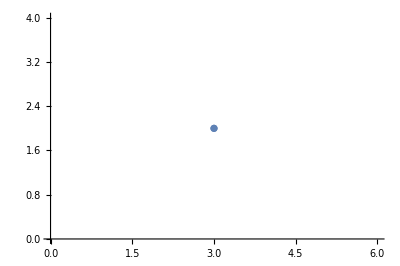

```mathematica
ComplexListPlot[{3 + 2I}]
```

Lahko se jih predstavi tudi kot:  z = x + iy = r(cos Fi + sin Fi), kjer je r = |z| in Fi = Arg(z). 
Dotaknili se bomo tudi kompleksne analize, natančneje holomorfne funkcije. To so funkcije, ki iz odprte podmnožice kompleksne ravnine slika v kompleksno ravnino in so odvedljive v kompleksnem v vsaki točki.
Pogledali si bomo tudo nalogo, pri kateri bomo z metodo ostankov izračunali integral po pozitivno orientirani krivulji.

## Naloge:

1. NALOGA:
Nariši množico kompleksnih števil, ki zadoščajo enačbi |z + 1| = |2z - 1|

Pišemo z = x + iy in računamo: 
|x + iy + 1| = |2x + 2iy - 1|
Sqrt((x + 1)^2 + y^2) = Sqrt((2x - 1)^2 + 4y^2)
x^2 + 2x + 1 + y^2 = 4 x^2 - 4x + 1 + 4y^2
1 = (x - 1)^2 + y^2 
Vidimo, da je to krožnica s središčem S(1,0) in polmerom r = 1.

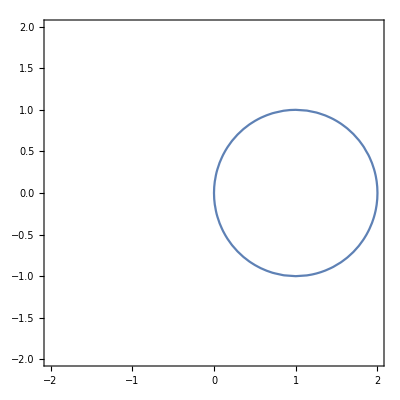

```mathematica
ComplexContourPlot[Abs[z+1]==Abs[2z-1],{z,-2-2 I,2+2 I}]
```

2. NALOGA:
Skiciraj podmnožico kompleksnih števil {Pi/4 < arg(z) <= Pi,  1 < |z| <= 2}.
Pomisli kako bi izgledalo, če ne bi imeli pogoja za |z|.

Neenakost 1 < |z| <= 2 določa kolobar z noranjim polemrom r = 1 in zunanjim R = 2. Neenakost Pi/4 < arg(z) <= Pi pa izreže krožni izsek.

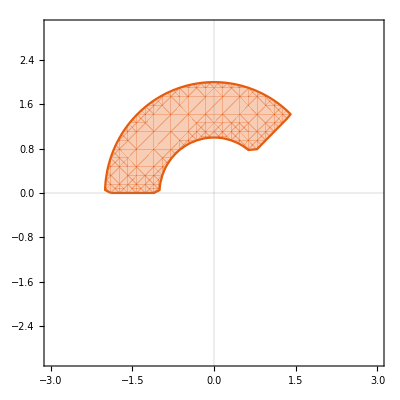

```mathematica
ComplexRegionPlot[1<Abs[z]≤2  && Pi/4<Arg[z]≤Pi, {z,-3 - 3I, 3 +3I}, PlotTheme-> "Scientific"]
```

Če ne bi imeli podanega pogoja za |z|, bi izgledalo takole:

```mathematica
Manipulate[ComplexRegionPlot[0<Abs[z]≤n && Pi/4<Arg[z]≤Pi, {z,-5 - I, 5 +10I}],{n, 0, 5}]
```

3. NALOGA:
Katera kompleksna števila zadoščajo pogojem: Re(z^2 - 2) < n in Im(z^2) < n, za n = 1. Prikaži grafično.
Katera števila bi zadoščala za splošen |n| <= 2

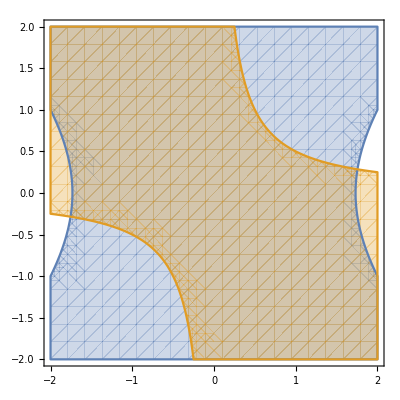

```mathematica
ComplexRegionPlot[{Re[z^2 - 2]< 1, Im[z^2] < 1},{z,2}]
```

```mathematica
Manipulate[ComplexRegionPlot[{Re[z^2 - 2]< n, Im[z^2] < n},{z,2}],{n, -2, 2}]
```

4. NALOGA:
Z metodo ostankov (residumov) izračunajre integral od 1/(z^4 + 1) po pozitivno orientirani krivulji |z - 1| = 1.   (-Graphics-)

Podintegralska funkcija f(z) = 1/(z^4 + 1) ima štiri enostavne pole, rešitve enačbe z^4 = -1. To so: z_k = e^(i(2k + 1)Pi/4) = cos(2k + 1)Pi/4 + sin(i(2k + 1)Pi/4) , k = 0,1,2,3.

```mathematica
nicle = ComplexListPlot[Callout[#, #] & /@ Table[E^(π I (2 k + 1)/4), {k, 0, 3}]]
```

-Graphics-

Vidimo, da znotraj krožnice |z - 1| = 1 ležita z_0 = e^(i Pi/4) in z_3 = e^(-i Pi/4).
Slika:      -Graphics-
Ostanka funkcije f(z) v teh dveh polih sta:

Res(f(z), z_0) = 1/(4 z_0^3) = e^(- i 3Pi/4) /4
Res(f(z), z_3) = 1/(4 z_3^3) = e^(i 3Pi/4) /4

Torej je-Graphics-
Ker je (e^(i 3Pi/4) + e^(- i 3Pi/4))/2 = cos(3Pi/4) = -Sqrt(2)/2, je končnen rezultat enak -Graphics-

5.NALOGA:
Poišči sliko kolobarja 1 < |z| < 2 s preslikavo w = f(z) = z/ (z-1)

Izrazimo inverzno funkcijo in dobimo z = f^-1(w) = w/ (w-1).
Ker imamo pogoj 1 < |z| < 2, vemo, da sta enačbi notranje in zunanje mejne krožnice kolobarja:-Graphics-
Ko vstavimo z = w/ (w-1) v zgornji enačbi, dobimo -Graphics-iz katerih dobimo enačbi: -Graphics-Če rečemo, da je w = u + iv, dobimo: -Graphics-

Poglejmo si kako je izgledal prej: 1 < |z| < 2

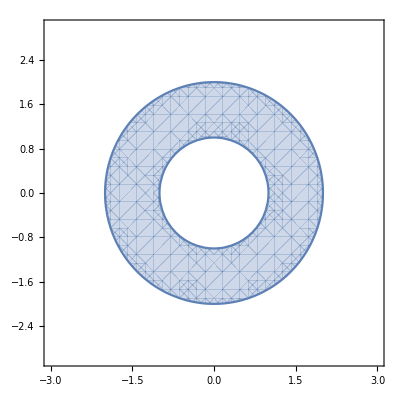

```mathematica
ComplexRegionPlot[1<Abs[z]≤2 ,{z,-3 - 3I, 3 +3I}]
```

in sedaj preslikano s preslikavo w = f(z) = z/(z-1)

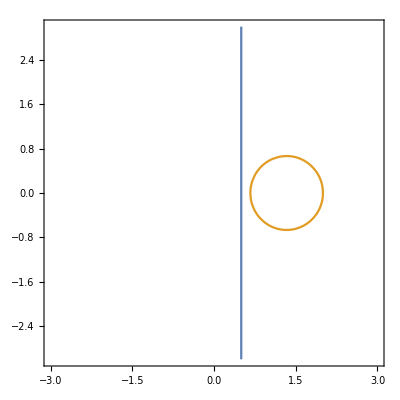

```mathematica
ContourPlot[{2 x==1, 3 x^2 + 3 y^2 - 8 x + 4==0 },{x, -3, 3},{y,-3, 3}]
```

Točka z = 3/2 je znotraj kolobarja in se preslika v w = f(3/2) = 3 znotraj preslikanega območja. Prva krivulja je primeca u = 1/2, druga pa krožnica (u - 4/3)^2 + v^2 = 4/9